```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

## Series solution for α_0(z) at z = 1

```mathematica
D4=5 (464-890 z+405 z^2) a0'[z]+(-4032+18232 z-23530 z^2+9225 z^3) a0''[z]+36 (-1+z) z ((140-324 z+175 z^2) Derivative[3][a0][z]+z (28-53 z+25 z^2) Derivative[4][a0][z]);
```

We have four solutions with exponents (0, 5/6, 1, 7/6). We know that the trivial solutions are just 1 and log(z) which are simply the ones corresponding to exponents 0 and 1 respectively.

```mathematica
Simplify[D4/.a0->Function[z,Log[z]]]
```

0

```mathematica
Series[Log[z], {z,1,10}]
```

(z-1)-1/2 (z-1)^2+1/3 (z-1)^3-1/4 (z-1)^4+1/5 (z-1)^5-1/6 (z-1)^6+1/7 (z-1)^7-1/8 (z-1)^8+1/9 (z-1)^9-1/10 (z-1)^10+O[z-1]^11

## Case 1: r = 5/6

```mathematica
(* recurrence *)
rec1 = a[n]==(25 (65-69 n+18 n^2)^2 a[-3+n]+(85099-227943 n+225657 n^2-97308 n^3+15228 n^4) a[-2+n]+3 (1344-10942 n+19185 n^2-11844 n^3+2052 n^4) a[-1+n])/(9 n (5-39 n+36 n^2+108 n^3));
```

```mathematica
coef1=Simplify[RecurrenceTable[{rec1,a[0]==1,a[1]==-41/66,a[2]==1537/3366}, a, {n,0,100}]];
```

```mathematica
Clear[a0Sol1];
a0Sol1[z_]=(z-1)^(5/6)coef1.((z-1)^Range[0, Length[coef1]-1]);
```

```mathematica
Simplify[Series[D4/.a0->Function[z, Evaluate[a0Sol1[z]]], {z,1,99}]]
```

O[z-1]^(595/6)

## Case 2: r = 7/6

```mathematica
(* recurrence *)
rec2 = a[n]==(25 (44-57 n+18 n^2)^2 a[-3+n]+(30775-107685 n+138501 n^2-77004 n^3+15228 n^4) a[-2+n]+3 (-585-1796 n+8709 n^2-9108 n^3+2052 n^4) a[-1+n])/(9 n (7+69 n+180 n^2+108 n^3));
```

```mathematica
coef2=Simplify[RecurrenceTable[{rec2,a[0]==1,a[1]==-2/3,a[2]==751/1482}, a, {n,0,100}]];
```

```mathematica
Clear[a0Sol2];
a0Sol2[z_]=(z-1)^(7/6)coef2.((z-1)^Range[0, Length[coef2]-1]);
```

```mathematica
Simplify[Series[D4/.a0->Function[z, Evaluate[a0Sol2[z]]], {z,1,99}]]
```

O[z-1]^(595/6)

## Transition matrix from LV to branch point

```mathematica
Alpha0[el_]=C1+C2 Log[el]/3/(2Pi I)+C3 a0Sol1[-256/27el]+C4 a0Sol2[-256/27el];
```

```mathematica
ResourceFunction["Fro"]
```

magic

```mathematica
eqns={
512 b0[el]+3 (27+256 el) (27 a0'[el]+8 b0'[el]+27 el a0''[el]),
128 (15+128 el) b0[el]+(27+256 el) ((27+512 el) b0'[el]+el (27+256 el) b0''[el]),
c0[el]-((81 ((243-3456 el+65536 el^2) b0[el]-108 el (27+256 el) b0'[el]))/(64 (27+256 el)^2))
};
```

```mathematica
eq=Simplify[eqns[[2]]/.b0->Function[el,b0[-256/27el]]/.el->-27/256z]
```

-192 (-10+9 z) b0[z]-6912 (-1+z) ((-1+2 z) b0'[z]+(-1+z) z b0''[z])

```mathematica
magic[eq==0, b0, z, 1, Association]
```

{<|r→-1/6,a_0→1,a_1→-1/6,a_2→4/45,a_n→((3072-9216 n+6912 n^2) a_(-1+n))/(2304 n-6912 n^2)|>,<|r→1/6,a_0→1,a_1→-1/3,a_2→25/126,a_n→((768-4608 n+6912 n^2) a_(-1+n))/(-2304 n-6912 n^2)|>}

```mathematica
Simplify[((768-4608 n+6912 n^2) Subscript["a", -1+n])/(-2304 n-6912 n^2)/.{Subscript["a",n_]:>a[n]}/.{ n->n}]
```

-((1-3 n)^2 a[-1+n])/(3 n (1+3 n))

## Case 1: r = -1/6

```mathematica
rec1=a[n]==-((2-3 n)^2 a[-1+n])/(3 n (-1+3 n));
```

```mathematica
coef1=Simplify[RecurrenceTable[{rec1,a[0]==1}, a, {n,0,100}]];
```

```mathematica
Clear[a1Sol1];
a1Sol1[z_]=(z-1)^(-1/6)coef1.((z-1)^Range[0, Length[coef1]-1]);
```

```mathematica
Simplify[Series[eq/.b0->Function[z, Evaluate[a1Sol1[z]]], {z,1,6}]]
```

O[z-1]^(37/6)

## Case 2: r = 1/6

```mathematica
rec2=a[n]==-((1-3 n)^2 a[-1+n])/(3 n (1+3 n));
```

```mathematica
coef2=Simplify[RecurrenceTable[{rec2,a[0]==1}, a, {n,0,100}]];
```

```mathematica
Clear[a1Sol2];
a1Sol2[z_]=(z-1)^(1/6)coef2.((z-1)^Range[0, Length[coef2]-1]);
```

```mathematica
Simplify[Series[eq/.b0->Function[z, Evaluate[a1Sol2[z]]], {z,1,6}]]
```

O[z-1]^(37/6)

```mathematica
BW[.1+.1I]
```

0.321667

```mathematica
MachinePrecision
```

```mathematica
tauB[.2+.1I]
```

0.137823+1.47817 ⅈ

```mathematica
InverseJ[.3+.2I]
```

-0.484805+0.87911 ⅈ

```mathematica
MatrixPower[{{1,0,0},{x,-1,0},{y,0,-1}}, 2]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
N[-256/27]
```

-9.48148

## Monodromies / Transition matrices

```mathematica
Options[ComputeTransition2Primitive]={WorkingPrecision->60};
ComputeTransition2Primitive[el_,upath_,Nn_:512,Nr_:5,OptionsPattern[]]:=Module[{sol,Psi0, Psi,mon,msg,tt=0},
Monitor[
msg="Solving for the system matrix...";
Psi0=SystemMatrix2[F1Series2[el,upath[0],Nn,Nr],el,upath[0]];
msg="Integrating the connection...";
sol=NDSolve[{Psi'[t]==upath'[t]*PicardFuchsA2[el,upath[t]].Psi[t],Psi[0]==Psi0},Psi,{t,0,1},WorkingPrecision->OptionValue[WorkingPrecision],MaxSteps->10^7,StepMonitor:>(tt=t)];
Psi[1]/. First[sol],
msg<>" "<>ToString[Floor[100 tt]]<>"%."]];
```

```mathematica
Options[ComputeTransition2]={WorkingPrecision->60};
ComputeTransition2[el_,upath_,Nn_:512,Nr_:5,OptionsPattern[]]:=Module[{sol,Psi,mon,SystMat,msg,tt=0},
Monitor[
msg="Integrating the connection...";
sol=NDSolve[{Psi'[t]==upath'[t]*PicardFuchsA2[el,upath[t]].Psi[t],Psi[0]==IdentityMatrix[3]},Psi,{t,0,1},WorkingPrecision->OptionValue[WorkingPrecision],MaxSteps->10^7,StepMonitor:>(tt=t)];
mon=Psi[1]/. First[sol];
msg="Solving for the system matrix...";
SystMat=SystemMatrix2[F1Series2[el,upath[0],Nn,Nr],el,upath[0]];
LinearSolve[SystMat,mon.SystMat],msg<>" "<>ToString[Floor[100 tt]]<>"%."]];
```

```mathematica
u0=ur/.Solve[MirrorCurveDelta2[1,ur]==0,ur]
```

{,,,}

```mathematica
upath=Interpolation[{{0,I/10},{1/2-1/5,#+I/10}, {1/2,#-1/10}, {1/2+1/5,#-I/10}, {1,I/10}}&[-8/9], PeriodicInterpolation->True];
upath1[t_]:=(1-t)I/10+t (-8/9);
```

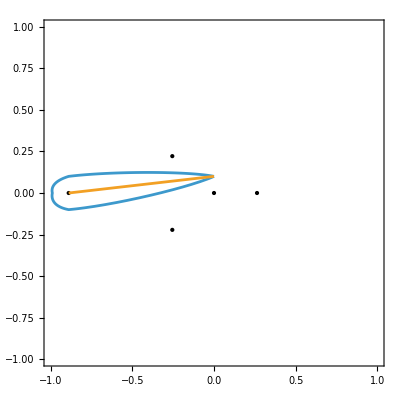

```mathematica
Show[{
Graphics[{Point[ReIm/@Join[u0, {0, -8/9}]]}],
ParametricPlot[Evaluate[ReIm/@{upath[t], upath1[t]}],{t,0,1}]
},
PlotRange->{{-1,1},{-1,1}},
AspectRatio->Automatic,
Axes->True,
Frame->True
]
```

```mathematica
temp=ComputeTransition2[1, upath, 512,5, WorkingPrecision->50]
```

{{1.,-2.7426407686992530865486748818463527309814229692×10^-22+1.12055425033106542906647483349481100115351142755×10^-21 ⅈ,-6.40571998869087600340855073039225690259773308904×10^-21+5.3487862080782042788441064495603420562235668378×10^-21 ⅈ},{0,0.99999999999999999999927019683549612264700184852-5.12037155371621325675744717×10^-21 ⅈ,1.7735990526956483004380674930599242039397161679×10^-20-3.29139372774651710406601294555433645038457634478×10^-20 ⅈ},{0,5.0510886087475967342075094168572508399205618099×10^-22+1.13962742819571774706332746345805301243038326629×10^-21 ⅈ,0.999999999999999999998047830132716080696998749274+8.787656411338668297555586111×10^-21 ⅈ}}

```mathematica
N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

```mathematica
a2=ComputeTransition2Primitive[1, upath1, 512,5, WorkingPrecision->50]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::nlnum: The function value {0,0.0087135559340314821874342259529724422735696358947507-0.077453830524724286110524682472790746913510206337336 ⅈ,0.1219089687800780373059553118662267262981193106104-0.30002166328145253222952309386041770498672444088576 ⅈ,0,«57»-«56» ⅈ,«71»-«56» ⅈ,Indeterminate,Indeterminate,Indeterminate} is not a list of numbers with dimensions {9} at {t,Psi$56367[t]} = {1.,{{1.,0.50000000000000000000000033655973419490865835002213+0.056294368673349473245005346300921616313482906055983 ⅈ,1.200683206745646663761386744512254122394167150501+0.22517747469339789298002314123128109561768334688666 ⅈ},«1»,{0,«1»,-0.20984557828367408941342654409052459339305399318529+«1»}}}.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{1.,0.500000000000000000000000336559734194908658350022+0.056294368673349473245005346300921616313482906056 ⅈ,1.2006832067456466637613867445122541223941671505+0.225177474693397892980023141231281095617683346887 ⅈ},{0,-2.2127116819616876378819765×10^-25+0.0871355593403148218743402926748960123466849083017 ⅈ,-0.0979365881744461221257467272658376929960210213358+0.348542237361259287497359987410376658572117360897 ⅈ},{0,-4.87135338495591109857422732873904013812541795704×10^-25+0.186702561113015548106194767679399102853309285234 ⅈ,-0.209845578283674089413426544090524593393053993185+0.746810244452062192424776523821479323020730409283 ⅈ}}

```mathematica
a2p=N[Chop[a2],20]
```

{{1.,0.5+0.05629436867334947325 ⅈ,1.2006832067456466638+0.225177474693397893 ⅈ},{0,0.087135559340314821874 ⅈ,-0.09793658817444612213+0.3485422373612592875 ⅈ},{0,0.18670256111301554811 ⅈ,-0.2098455782836740894+0.74681024445206219242 ⅈ}}

```mathematica
a2p[[2,3]]/a2p[[2,2]]
```

4.+1.123956613303496767 ⅈ

l = -27/256

```mathematica
u0=ur/.Solve[MirrorCurveDelta2[-27/256,ur]==0,ur]
```

{-8/9,-8/9,8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2)}

```mathematica
upath=Interpolation[{{0,I/10},{1/2-1/5,#+I/10}, {1/2,#-1/10}, {1/2+1/5,#-I/10}, {1,I/10}}&[-8/9], PeriodicInterpolation->True];
upath1[t_]:=(1-t)I/10+t (-8/9+10^-5);
```

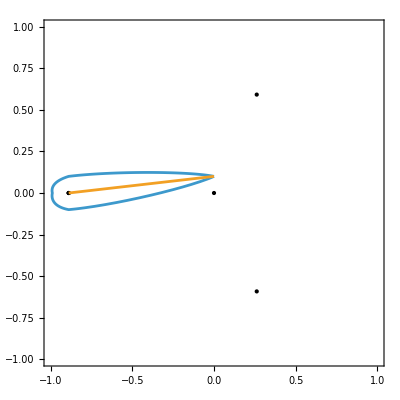

```mathematica
Show[{
Graphics[{Point[ReIm/@Join[u0, {0, -8/9}]]}],
ParametricPlot[Evaluate[ReIm/@{upath[t], upath1[t]}],{t,0,1}]
},
PlotRange->{{-1,1},{-1,1}},
AspectRatio->Automatic,
Axes->True,
Frame->True
]
```

```mathematica
temp=ComputeTransition2[-27/256, upath, 512,5, WorkingPrecision->50]
```

{{1.,-1.3333333333333333333332699974568957499342183804+0.1193312239205055688633077464902970361885500095 ⅈ,-8.6666666666666666666664886902719283003994223885+0.5966561196025278443166661598546214618016255231 ⅈ},{0,5.999999999999999999999757760612940557167722835-3.149857363523713655720378×10^-22 ⅈ,30.999999999999999999999149250813072023294846285-2.032784342782949836114138×10^-21 ⅈ},{0,-0.99999999999999999999994689063441044545296539757+5.197369130137248956849366×10^-23 ⅈ,-4.9999999999999999999997818526447594574516252457+3.446294990657808767474938×10^-22 ⅈ}}

```mathematica
a1=N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{-1.33333+0.119331 ⅈ,6.,-1.},{-8.66667+0.596656 ⅈ,31.,-5.}}

```mathematica
MonodromyFromSphericalTwist[Ch[0,1]/.repCh].MonodromyFromSphericalTwist[GV[0,1,1/2]/.repCh]
```

{{1,0,0,0},{0,1,0,0},{1,0,1,-1},{1/2,-1,1,0}}

```mathematica
a2=ComputeTransition2Primitive[-27/256, upath1, 256,3, WorkingPrecision->20]
```

{{1.,0.6666666667358715893+0.119346663844600921 ⅈ,1.999986426764921345+0.7160722636411241451 ⅈ},{0,-7.001323×10^-10+1.28278785892197 ⅈ,-1.13454184435157+7.0553332218286 ⅈ},{0,0.00005413009-21831.933443208 ⅈ,18513.376908062-120075.63386282 ⅈ}}

```mathematica
a2p=N[Chop[a2],20]
```

{{1.,0.6666666667358715893+0.119346663844600921 ⅈ,1.999986426764921345+0.7160722636411241451 ⅈ},{0,-7.001323×10^-10+1.28278785892197 ⅈ,-1.13454184435157+7.0553332218286 ⅈ},{0,0.00005413009-21831.933443208 ⅈ,18513.376908062-120075.63386282 ⅈ}}

```mathematica
a2p[[2,3]]/a2p[[2,2]]
```

5.49999999873475+0.884434501472663 ⅈ

l = -27/256

```mathematica
u0=ur/.Solve[MirrorCurveDelta2[-27/256,ur]==0,ur]
```

{-8/9,-8/9,8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2)}

```mathematica
upath=Interpolation[{{0,I/10},{1/2-1/5,#+I/10}, {1/2,#-1/10}, {1/2+1/5,#-I/10}, {1,I/10}}&[-8/9], PeriodicInterpolation->True];
upath1[t_]:=(1-t)I/10+t (-8/9+10^-5);
```

```mathematica
Show[{
Graphics[{Point[ReIm/@Join[u0, {0, -8/9}]]}],
ParametricPlot[Evaluate[ReIm/@{upath[t], upath1[t]}],{t,0,1}]
},
PlotRange->{{-1,1},{-1,1}},
AspectRatio->Automatic,
Axes->True,
Frame->True
]
```

-Graphics-

```mathematica
temp=ComputeTransition2[-27/256, upath, 512,5, WorkingPrecision->50]
```

{{1.,-1.3333333333333333333332699974568957499342183804+0.1193312239205055688633077464902970361885500095 ⅈ,-8.6666666666666666666664886902719283003994223885+0.5966561196025278443166661598546214618016255231 ⅈ},{0,5.999999999999999999999757760612940557167722835-3.149857363523713655720378×10^-22 ⅈ,30.999999999999999999999149250813072023294846285-2.032784342782949836114138×10^-21 ⅈ},{0,-0.99999999999999999999994689063441044545296539757+5.197369130137248956849366×10^-23 ⅈ,-4.9999999999999999999997818526447594574516252457+3.446294990657808767474938×10^-22 ⅈ}}

```mathematica
N[Chop[temp]]ᵀ
```

{{1.,0.,0.},{-1.33333+0.119331 ⅈ,6.,-1.},{-8.66667+0.596656 ⅈ,31.,-5.}}

```mathematica
a2=ComputeTransition2Primitive[-27/256, upath1, 256,3, WorkingPrecision->20]
```

{{1.,0.6666666667358715893+0.119346663844600921 ⅈ,1.999986426764921345+0.7160722636411241451 ⅈ},{0,-7.001323×10^-10+1.28278785892197 ⅈ,-1.13454184435157+7.0553332218286 ⅈ},{0,0.00005413009-21831.933443208 ⅈ,18513.376908062-120075.63386282 ⅈ}}

```mathematica
a2p=N[Chop[a2],20]
```

{{1.,0.6666666667358715893+0.119346663844600921 ⅈ,1.999986426764921345+0.7160722636411241451 ⅈ},{0,-7.001323×10^-10+1.28278785892197 ⅈ,-1.13454184435157+7.0553332218286 ⅈ},{0,0.00005413009-21831.933443208 ⅈ,18513.376908062-120075.63386282 ⅈ}}

```mathematica
a2p[[2,3]]/a2p[[2,2]]
```

5.49999999873475+0.884434501472663 ⅈ

```mathematica
N[1/Last[coef1^(1/Range[0,Length[coef1]-1])],10]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1^ComplexInfinity encountered.

1.037874108

## Can apparent singularities be removed

```mathematica
PicardFuchsP2[el,ur]
```

(24+50 ur+(27-320 el) ur^2-2016 el ur^3+4 el (-783+224 el) ur^4+54 el (-27+16 el) ur^5)/(ur (8+9 ur) (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4))

```mathematica
PicardFuchsQ2[el,ur]
```

(8+16 ur+(9-256 el) ur^2-1860 el ur^3+16 el (-189+64 el) ur^4+54 el (-27+16 el) ur^5)/(ur^2 (8+9 ur) (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4))

```mathematica
ps=Simplify@Series[PicardFuchsP2[el,ur], {ur,-8/9,1}]
```

-1/(ur+8/9)+(1215-16128 el)/(216+2048 el)-(81 (48843+13824 el+458752 el^2) (ur+8/9))/(64 (27+256 el)^2)+O[ur+8/9]^2

```mathematica
qs=Simplify@Series[PicardFuchsQ2[el,ur], {ur,-8/9,1}]
```

(9 (27+512 el))/(8 (27+256 el) (ur+8/9))+(81 (27+512 el) (-81+640 el))/(32 (27+256 el)^2)+(6561 (129033+2840832 el+33554432 el^3) (ur+8/9))/(512 (27+256 el)^3)+O[ur+8/9]^2

```mathematica
Simplify[qs[[3,2]]+ps[[3,2]]*qs[[3,1]]+qs[[3,1]]^2]
```

0

```mathematica
sol={
a2->(a1 qm1)/2
};
```

```mathematica
F'''[z]+(-1/z+p0+p1 z+p2 z^2+p3 z^3)F''[z]+(qm1/z+q0+q1 z+q2 z^2+q3 z^3)F'[z]
Simplify@Series[%/.F->Function[z, Evaluate[a1 z+a2 z^2+a4 z^4/.sol]], {z,0,1}]
```

(q0+qm1/z+q1 z+q2 z^2+q3 z^3) F'[z]+(p0-1/z+p1 z+p2 z^2+p3 z^3) F''[z]+F^(3)[z]

a1 (q0+qm1 (p0+qm1))+(12 a4+a1 (q1+(p1+q0) qm1)) z+O[z]^2

```mathematica
Solve[-2 a2+a1 qm1==0,a2]
```

{{a2→(a1 qm1)/2}}

```mathematica
Solve[(-1+s) s (-2+pm1+s)==0,s]
```

{{s→0},{s→1},{s→2-pm1}}

```mathematica
Simplify[{w'[z],w''[z],w'''[z]}/.{w->InverseFunction[z]}]/.{(z^(-1))[z]->w}
repwd=Thread[{w'[z],w''[z],w'''[z]}->%];
```

{1/z'[w],-z''[w]/z'[w]^3,(3 z''[w]^2-z'[w] z^(3)[w])/z'[w]^5}

```mathematica
Simplify[Simplify[{F'[z],F''[z],F'''[z]}/.{F->Function[z, G[w[z]]]}]/.repwd/.{w[z]->w}][[3]]
Simplify@Coefficient[%, {Derivative[3][G][w], Derivative[2][G][w], Derivative[1][G][w]}]
```

(3 G'[w] z''[w]^2+z'[w]^2 G^(3)[w]-z'[w] (3 G''[w] z''[w]+G'[w] z^(3)[w]))/z'[w]^5

{1/z'[w]^3,-(3 z''[w])/z'[w]^4,(3 z''[w]^2-z'[w] z^(3)[w])/z'[w]^5}

```mathematica
Simplify[Simplify[F'''[z]+P[z]*F''[z]+Q[z]*F'[z]/.{F->Function[z, G[w[z]]]}]/.repwd/.{w[z]->w}]
Simplify[Coefficient[%, {G''[w],G'[w],G[w]}]/Coefficient[%, G'''[w]]]/.{P[z]->P[z[w]], Q[z]->Q[z[w]]}
```

1/z'[w]^5(Q[z] G'[w] z'[w]^4-3 z'[w] G''[w] z''[w]+3 G'[w] z''[w]^2+P[z] z'[w]^2 (z'[w] G''[w]-G'[w] z''[w])+z'[w]^2 G^(3)[w]-G'[w] z'[w] z^(3)[w])

{P[z[w]] z'[w]-(3 z''[w])/z'[w],Q[z[w]] z'[w]^2-P[z[w]] z''[w]+(3 z''[w]^2-z'[w] z^(3)[w])/z'[w]^2,0}

```mathematica
P[z[w]] z'[w]-(3 z''[w])/z'[w]/.{P->Function[z, -1/z+p0+p1 z]}/.{z->Function[w, a2 w^(3/4)]}
Series[%, {w,0,1}]
```

3/(4 w)+(3 a2 (p0-1/(a2 w^(3/4))+a2 p1 w^(3/4)))/(4 w^(1/4))

(3 a2 p0)/(4 w^(1/4))+3/4 a2^2 p1 √w+O[w]^(5/4)

```mathematica
With[{n=1},(3-3 n+n pm1)/w]
```

pm1/w

```mathematica
Solve[3-3 n+n pm1==0,n]/.{pm1->-1}
```

{{n→3/4}}

```mathematica
Simplify[D[PicardFuchs2[f[el,ur],el,ur], ur]]
Simplify[Coefficient[%, {Derivative[0,4][f][el,ur], Derivative[0,3][f][el,ur], Derivative[0,2][f][el,ur], Derivative[0,1][f][el,ur]}]/Coefficient[%, Derivative[0,4][f][el,ur]]]
```

(-((128+536 ur-64 (-13+32 el) ur^2+(585-6944 el) ur^3+2 (81-3168 el+11264 el^2) ur^4+4 el (783+93920 el) ur^5+4 el (1701+470304 el-32768 el^2) ur^6-9 el (-243-479808 el+134656 el^2) ur^7+16 el^2 (317115-184464 el+16384 el^2) ur^8+216 el^2 (13851-12528 el+2560 el^2) ur^9+972 (27-16 el)^2 el^2 ur^10) f^(0,1)[el,ur])+ur ((-128-552 ur-2 (433+256 el) ur^2-(603+14432 el) ur^3+2 (-81-27402 el+5632 el^2) ur^4+4 el (-21087+5024 el) ur^5-2 el (29403+4608 el+16384 el^2) ur^6-3 el (5103+14688 el+36352 el^2) ur^7+4 el^2 (-6561-18576 el+4096 el^2) ur^8) f^(0,2)[el,ur]+ur (8+9 ur) (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4) ((24+50 ur+(27-320 el) ur^2-2016 el ur^3+4 el (-783+224 el) ur^4+54 el (-27+16 el) ur^5) f^(0,3)[el,ur]+ur (8+9 ur) (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4) f^(0,4)[el,ur])))/(ur^3 (8+9 ur)^2 (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4)^2)

{1,(24+50 ur+(27-320 el) ur^2-2016 el ur^3+4 el (-783+224 el) ur^4+54 el (-27+16 el) ur^5)/(ur (8+9 ur) (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4)),-((128+552 ur+(866+512 el) ur^2+(603+14432 el) ur^3+(162+54804 el-11264 el^2) ur^4+4 (21087-5024 el) el ur^5+2 el (29403+4608 el+16384 el^2) ur^6+3 el (5103+14688 el+36352 el^2) ur^7+4 el^2 (6561+18576 el-4096 el^2) ur^8)/(ur^2 (8+9 ur)^2 (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4)^2)),(-128-536 ur+64 (-13+32 el) ur^2+(-585+6944 el) ur^3-2 (81-3168 el+11264 el^2) ur^4-4 el (783+93920 el) ur^5+4 el (-1701-470304 el+32768 el^2) ur^6+9 el (-243-479808 el+134656 el^2) ur^7-16 el^2 (317115-184464 el+16384 el^2) ur^8-216 el^2 (13851-12528 el+2560 el^2) ur^9-972 (27-16 el)^2 el^2 ur^10)/(ur^3 (8+9 ur)^2 (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4)^2)}

```mathematica
Simplify[D[Simplify[Denominator[PicardFuchsQ2[el,ur]]*PicardFuchs2[f[el,ur],el,ur]], ur]]
Simplify[Coefficient[%, {Derivative[0,4][f][el,ur], Derivative[0,3][f][el,ur], Derivative[0,2][f][el,ur], Derivative[0,1][f][el,ur]}]/Coefficient[%, Derivative[0,4][f][el,ur]]]
```

2 (8+(9-256 el) ur-2790 el ur^2+32 el (-189+64 el) ur^3+135 el (-27+16 el) ur^4) f^(0,1)[el,ur]+2 (16+58 ur+(45-608 el) ur^2-4962 el ur^3+2 el (-4671+1376 el) ur^4+189 el (-27+16 el) ur^5) f^(0,2)[el,ur]+ur (8+9 ur) ((5+7 ur-72 el ur^2-396 el ur^3+13 el (-27+16 el) ur^4) f^(0,3)[el,ur]+ur (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4) f^(0,4)[el,ur])

{1,(5+7 ur-72 el ur^2-396 el ur^3+13 el (-27+16 el) ur^4)/(ur (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4)),(2 (16+58 ur+(45-608 el) ur^2-4962 el ur^3+2 el (-4671+1376 el) ur^4+189 el (-27+16 el) ur^5))/(ur^2 (8+9 ur) (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4)),(2 (8+(9-256 el) ur-2790 el ur^2+32 el (-189+64 el) ur^3+135 el (-27+16 el) ur^4))/(ur^2 (8+9 ur) (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4))}

```mathematica
Simplify[Denominator[PicardFuchsQ2[el,ur]]*PicardFuchs2[f[el,ur],el,ur]]
```

(8+16 ur+(9-256 el) ur^2-1860 el ur^3+16 el (-189+64 el) ur^4+54 el (-27+16 el) ur^5) f^(0,1)[el,ur]+ur ((24+50 ur+(27-320 el) ur^2-2016 el ur^3+4 el (-783+224 el) ur^4+54 el (-27+16 el) ur^5) f^(0,2)[el,ur]+ur (8+9 ur) (1+ur-8 el ur^2-36 el ur^3+el (-27+16 el) ur^4) f^(0,3)[el,ur])

```mathematica
magic=ResourceFunction["FrobeniusDSolveFormula"]
```

```mathematica
eq=Simplify[Simplify[(x^2 (8+9 x) (1+x-8 l x^2-36 l x^3+l (-27+16 l) x^4))PicardFuchs2[F[x],l,x]]/.{l->-256/27z}]
```

(8+16 x+(158720 x^3 z)/9+x^2 (9+(65536 z)/27)+512/27 x^5 z (729+4096 z)+4096/729 x^4 z (5103+16384 z)) F'[x]+1/729 x ((17496+36450 x+13934592 x^3 z+13824 x^5 z (729+4096 z)+1024 x^4 z (21141+57344 z)+27 x^2 (729+81920 z)) F''[x]+x (8+9 x) (729+729 x+55296 x^2 z+248832 x^3 z+256 x^4 z (729+4096 z)) F^(3)[x])

```mathematica
res=magic[eq==0,F,x,-8/9,Association];
```

```mathematica
magic[x(1-x-l)f'[x]-l f[x]==0,f,x,0,Association]
```

{<|r→-l/(-1+l),a_0→1,a_1→l/(-1+l)^2,a_n→((-1+n-l/(-1+l)) a_(-1+n))/(n-l-n l-l/(-1+l)+l^2/(-1+l))|>}

```mathematica
Subscript[a,n]
```

a_n

```mathematica
Simplify[res[[2]][Subscript[a,n]]/.{n->n}]
```

(59049 (-9 l (-27+16 l) (-60+47 n-12 n^2+n^3) a_(-6+n)+4 l (12-7 n+n^2) (783-243 n+32 l (-19+6 n)) a_(-5+n)-4/9 l (-3+n) (256 l (108-80 n+15 n^2)-27 (947-686 n+126 n^2)) a_(-4+n)+1/81 (-2+n) (-729 (-2+n)^2+16384 l^2 (51-45 n+10 n^2)-864 l (579-486 n+104 n^2)) a_(-3+n)-1/729 (-1+n) (65536 l^2 (48-55 n+15 n^2)-729 (46-53 n+15 n^2)-6912 l (141-142 n+36 n^2)) a_(-2+n)+(8 (27+256 l) n (-27 (14-19 n+6 n^2)+256 l (9-17 n+6 n^2)) a_(-1+n))/6561))/(64 (27+256 l)^2 n (-2-n+n^2))

## Full expansion at u = -8/9

```mathematica
magic=ResourceFunction["FrobeniusDSolveFormula"]
```

We use
x = ur + 8/9
t = -256/27 el - 1

```mathematica
den=((8-9 x)^2 x (t^2 (8-9 x)^4+54 t (8-9 x)^2 x (-16+27 x)+729 x^2 (256-352 x+153 x^2)));
```

```mathematica
PF3=Simplify@Expand[den*PicardFuchs2[F[l,u],l,u]/.{F->Function[{l,u}, F[-256/27l-1, u+8/9]]}/.{l->-27/256(t+1),u->-8/9+x}]
```

18 (t^2 (8-9 x)^4 (8+27 x)+2 t (8-9 x)^2 (128-144 x-13608 x^2+19683 x^3)+9 x (-2048-140544 x+640224 x^2-810648 x^3+334611 x^4)) F^(0,1)[t,x]+(-8+9 x) (2 (t^2 (8-9 x)^4 (4+27 x)+486 t (8-9 x)^2 x^2 (-52+81 x)+729 x^2 (-1024+7424 x-9756 x^2+4131 x^3)) F^(0,2)[t,x]+x (-8+9 x) (t^2 (8-9 x)^4+54 t (8-9 x)^2 x (-16+27 x)+729 x^2 (256-352 x+153 x^2)) F^(0,3)[t,x])

```mathematica
Simplify@Series[PF3/.{F->Function[{t,x}, x^s]}, {x,0,0}]
```

x^s ((262144 s (3-4 s+s^2) t^2)/x^2+1/O[x])

```mathematica
eq=PF3==0/.{F->Function[{t,x},F[x]]};
res=magic[eq, F, x, 0, Association];
```

```mathematica
Simplify[res[[2]][Subscript[a,5]]]
```

(6561 (59868565185+275554798090 t+528722562940 t^2+552570530808 t^3+347599519893 t^4+139261096926 t^5+36530355654 t^6+6418638072 t^7+830383488 t^8+119688192 t^9+22083840 t^10+2239488 t^11))/(1048576 t^5 (10082195+1773260 t-1476621 t^2-450234 t^3+132408 t^4+84672 t^5+12096 t^6))

```mathematica
Simplify[res[[2]][Subscript[a,n]]/.{n->n}/.Subscript["a",n_]:>a[n]]
```

1/(262144 n (-2-n+n^2) t^2)(-531441 (-60+47 n-12 n^2+n^3) (17+18 t+t^2) a[-6+n]+72 (6561 (12-7 n+n^2) (1+t) (-251-19 t+6 n (13+t)) a[-5+n]-5832 (-3+n) (1+t) (1055+108 t+3 n^2 (47+5 t)-2 n (383+40 t)) a[-4+n]+64 (81 (-2+n) (649+783 t+102 t^2+4 n^2 (29+36 t+5 t^2)-2 n (272+333 t+45 t^2)) a[-3+n]-72 (-1+n) (143+237 t+48 t^2+3 n^2 (12+22 t+5 t^2)-n (144+252 t+55 t^2)) a[-2+n]+64 n t (23+9 t+6 n^2 (2+t)-n (36+17 t)) a[-1+n])))

```mathematica
RecData1[t_]:={
a[n]==1/(262144 n (-2-n+n^2) t^2)(-531441 (-60+47 n-12 n^2+n^3) (17+18 t+t^2) a[-6+n]+72 (6561 (12-7 n+n^2) (1+t) (-251-19 t+6 n (13+t)) a[-5+n]-5832 (-3+n) (1+t) (1055+108 t+3 n^2 (47+5 t)-2 n (383+40 t)) a[-4+n]+64 (81 (-2+n) (649+783 t+102 t^2+4 n^2 (29+36 t+5 t^2)-2 n (272+333 t+45 t^2)) a[-3+n]-72 (-1+n) (143+237 t+48 t^2+3 n^2 (12+22 t+5 t^2)-n (144+252 t+55 t^2)) a[-2+n]+64 n t (23+9 t+6 n^2 (2+t)-n (36+17 t)) a[-1+n]))),
a[0]==1,
a[1]==9/16 (2+1/t),a[2]==0,a[3]==-(243 (35+84 t+87 t^2+24 t^3))/(2048 t^3),a[4]==-(2187 (2485+6272 t+6783 t^2+3024 t^3+600 t^4))/(163840 t^4),a[5]==-(6561 (17661+45878 t+50967 t^2+25722 t^3+8064 t^4+1296 t^5))/(524288 t^5)
};
```

```mathematica
GenRec[recdata_, nmax_]:=RecurrenceTable[recdata, a[n], {n,nmax}];
```

```mathematica
coef=Simplify@RecurrenceTable[RecData1[t], a[n], {n,15}];
```

```mathematica
Frob1[t_,x_,nmax_]:=Module[{coef},
coef=Simplify@RecurrenceTable[RecData1[t], a[n], {n,nmax}];
x(coef.x^Range[0, Length[coef]-1])
];
```

```mathematica
Simplify@Series[PF3/.F->Function[{t,x}, Evaluate[Frob1[t,x,15]]], {x,0,12}]
```

O[x]^13

```mathematica
Simplify[res[[3]][Subscript[a,n]]/.{n->n}/.Subscript["a",n_]:>a[n]]
```

1/(262144 n (6+5 n+n^2) t^2)(-531441 (-6+11 n-6 n^2+n^3) (17+18 t+t^2) a[-6+n]+72 (6561 (2-3 n+n^2) (1+t) (-95-7 t+6 n (13+t)) a[-5+n]-5832 (-1+n) (1+t) (87+8 t+3 n^2 (47+5 t)-2 n (101+10 t)) a[-4+n]+64 (81 n (25+27 t+2 t^2-10 n (8+9 t+t^2)+4 n^2 (29+36 t+5 t^2)) a[-3+n]-72 (1+n) (-1-3 t-2 t^2+n t (12+5 t)+3 n^2 (12+22 t+5 t^2)) a[-2+n]+64 (2+n) t (-1-t+6 n^2 (2+t)+n (12+7 t)) a[-1+n])))

```mathematica
RecData2[t_]:={
a[n]==1/(262144 n (6+5 n+n^2) t^2)(-531441 (-6+11 n-6 n^2+n^3) (17+18 t+t^2) a[-6+n]+72 (6561 (2-3 n+n^2) (1+t) (-95-7 t+6 n (13+t)) a[-5+n]-5832 (-1+n) (1+t) (87+8 t+3 n^2 (47+5 t)-2 n (101+10 t)) a[-4+n]+64 (81 n (25+27 t+2 t^2-10 n (8+9 t+t^2)+4 n^2 (29+36 t+5 t^2)) a[-3+n]-72 (1+n) (-1-3 t-2 t^2+n t (12+5 t)+3 n^2 (12+22 t+5 t^2)) a[-2+n]+64 (2+n) t (-1-t+6 n^2 (2+t)+n (12+7 t)) a[-1+n]))),
a[0]==1,a[1]==(9 (23+12 t))/(32 t),a[2]==(81 (301+212 t+60 t^2))/(640 t^2),a[3]==(243 (1879+1398 t+582 t^2+120 t^3))/(2048 t^3),a[4]==(6561 (46001+30624 t+14067 t^2+4928 t^3+840 t^4))/(229376 t^4),a[5]==(59049 (278785+132608 t+44075 t^2+23384 t^3+8848 t^4+1344 t^5))/(2097152 t^5)
};
```

```mathematica
coef=Simplify@RecurrenceTable[RecData2[t], a[n], {n,15}];
```

```mathematica
Frob2[t_,x_,nmax_]:=Module[{coef},
coef=Simplify@RecurrenceTable[RecData2[t], a[n], {n,nmax}];
x^3(coef.x^Range[0, Length[coef]-1])
];
```

```mathematica
Simplify@Series[PF3/.F->Function[{t,x}, Evaluate[Frob2[t,x,15]]], {x,0,12}]
```

O[x]^13

outcomes: Frob1 and Frob2

#### Applying D1 and D2

```mathematica
PF1=Simplify[Expand[PicardFuchsD1[F[l,u],l,u]/.{F->Function[{l,u}, F[-256/27l-1, u+8/9]]}/.{l->-27/256(t+1),u->-8/9+x}]]
```

1/6561(-18 (-8+9 x)^3 F^(0,1)[t,x]-(8-9 x)^4 F^(0,2)[t,x]-6912 (27 F^(1,0)[t,x]+(8-9 x) F^(1,1)[t,x]+27 (1+t) F^(2,0)[t,x]))

```mathematica
PF2=Simplify[Expand[PicardFuchsD2[F[l,u],l,u]/.{F->Function[{l,u}, F[-256/27l-1, u+8/9]]}/.{l->-27/256(t+1),u->-8/9+x}]]
```

(-8/81-(7 x)/9+x^2) F^(0,1)[t,x]+1/729 ((8-9 x)^2 (1+9 x) F^(0,2)[t,x]+27 (1+t) (108 F^(1,0)[t,x]+(32+36 x-81 x^2) F^(1,1)[t,x]+108 (1+t) F^(2,0)[t,x]))

```mathematica
Comb=A0[t]+A1[t]*Frob1[t,x,10]+A2[t]*Frob2[t,x,10];
```

```mathematica
temp=Simplify@Series[PF1/.F->Function[{t,x},Evaluate[Comb]], {x,0,1}]
```

-(256 (2 A1[t]+3 t (27 A0'[t]+8 A1'[t]+27 (1+t) A0''[t])))/(729 t)-(128 (-81 (2+t+t^2) A1[t]+2 t (32 t A2[t]+81 ((1+4 t) A1'[t]+3 t (1+t) A1''[t]))) x)/(2187 t^2)+O[x]^2

```mathematica
eqns={
2 A1[t]+3 t (27 A0'[t]+8 A1'[t]+27 (1+t) A0''[t]),
(-1+9 t) A1[t]+36 t ((1+2 t) A1'[t]+t (1+t) A1''[t]),
A2[t]-(27 ((11+15 t+6 t^2) A1[t]+24 t (1+t) A1'[t]))/(128 t^2)
};
```

```mathematica
repA1dd=First@Simplify[Solve[eqns[[2]]==0,A1''[t]]]
```

{A1''[t]→((1-9 t) A1[t]-36 t (1+2 t) A1'[t])/(36 t^2 (1+t))}

```mathematica
deq=Simplify[D[eqns[[1]],t]/.repA1dd]
```

1/(3 t (1+t))((2-18 t) A1[t]+3 t (81 (1+t) A0'[t]+(2-22 t) A1'[t]+81 (1+t) ((1+3 t) A0''[t]+t (1+t) A0^(3)[t])))

```mathematica
ddeq=Simplify[D[deq,t]/.repA1dd]
```

1/(18 t^2 (1+t)^2)((-11-44 t+207 t^2) A1[t]+6 t (2 (-2-17 t+57 t^2) A1'[t]+243 t (1+t)^2 (4 A0''[t]+(2+5 t) A0^(3)[t]+t (1+t) A0^(4)[t])))

```mathematica
Simplify@Solve[Coefficient[ddeq+a deq+b eqns[[1]], {A1[t], A1'[t]}]==0,{a,b}]
A0eq1=Simplify[ddeq+a deq+b eqns[[1]]/.First[%]]
Simplify[Coefficient[%, {Derivative[4][A0][t], Derivative[3][A0][t], Derivative[2][A0][t], Derivative[1][A0][t]}]/Coefficient[%, Derivative[4][A0][t]]]
```

{{a→(3+9 t-50 t^2)/(3 t-22 t^2-25 t^3),b→(3-76 t+225 t^2)/(36 t^2 (1+t) (-3+25 t))}}

1/(4 t (1+t) (-3+25 t))9 (5 (-21-80 t+405 t^2) A0'[t]+(-105-1153 t+4145 t^2+9225 t^3) A0''[t]+36 t (1+t) ((-9+26 t+175 t^2) A0^(3)[t]+t (-3+22 t+25 t^2) A0^(4)[t]))

{1,(-9+26 t+175 t^2)/(t (1+t) (-3+25 t)),(-105-1153 t+4145 t^2+9225 t^3)/(36 t^2 (1+t)^2 (-3+25 t)),(5 (-21-80 t+405 t^2))/(36 t^2 (1+t)^2 (-3+25 t))}

```mathematica
A0eq=Simplify[A0eq1*(36 t^2 (1+t)^2 (-3+25 t))/Coefficient[A0eq1,Derivative[4][A0][t]]]
```

5 (-21-80 t+405 t^2) A0'[t]+(-105-1153 t+4145 t^2+9225 t^3) A0''[t]+36 t (1+t) ((-9+26 t+175 t^2) A0^(3)[t]+t (-3+22 t+25 t^2) A0^(4)[t])

```mathematica
res=magic[A0eq==0,A0,t,0,Association];
```

```mathematica
res[[2]]
```

<|r→5/6,a_0→1,a_1→-41/66,a_2→1537/3366,a_3→-127013/348381,a_4→18506569/60618294,a_5→-3356596141/12729841740,a_6→31233791893/134208902916,a_n→((-105625/9+(74750 n)/3-19725 n^2+6900 n^3-900 n^4) a_(-3+n)+(-85099/9+25327 n-25073 n^2+10812 n^3-1692 n^4) a_(-2+n)+(-448+(10942 n)/3-6395 n^2+3948 n^3-684 n^4) a_(-1+n))/(-5 n+39 n^2-36 n^3-108 n^4)|>

```mathematica
Simplify[res[[2]][Subscript[a,2]]]
```

1537/3366

```mathematica
Simplify[res[[2]][Subscript[a,n]]/.{n->n}/.Subscript["a",n_]:>a[n]]
```

(25 (65-69 n+18 n^2)^2 a[-3+n]+(85099-227943 n+225657 n^2-97308 n^3+15228 n^4) a[-2+n]+3 (1344-10942 n+19185 n^2-11844 n^3+2052 n^4) a[-1+n])/(9 n (5-39 n+36 n^2+108 n^3))

```mathematica
RecA01={
a[n]==(25 (65-69 n+18 n^2)^2 a[-3+n]+(85099-227943 n+225657 n^2-97308 n^3+15228 n^4) a[-2+n]+3 (1344-10942 n+19185 n^2-11844 n^3+2052 n^4) a[-1+n])/(9 n (5-39 n+36 n^2+108 n^3)),
a[0]==1,
a[1]==-41/66,
a[2]==1537/3366
};
```

```mathematica
A0Frob1[t_,nmax_]:=Module[{coef},
coef=Simplify@RecurrenceTable[RecA01, a[n], {n,nmax}];
t^(5/6)(coef.t^Range[0, Length[coef]-1])
];
```

```mathematica
Simplify@Series[A0eq/.A0->Function[t, Evaluate[A0Frob1[t,100]]], {t,0,98}]
```

O[t]^(589/6)

```mathematica
res[[4]]
```

<|r→7/6,a_0→1,a_1→-2/3,a_2→751/1482,a_3→-412303/1000350,a_4→6497209/18606510,a_5→-209299049/688440870,a_6→107864744413/399639925035,a_n→((-48400/9+(41800 n)/3-13425 n^2+5700 n^3-900 n^4) a_(-3+n)+(-30775/9+11965 n-15389 n^2+8556 n^3-1692 n^4) a_(-2+n)+(195+(1796 n)/3-2903 n^2+3036 n^3-684 n^4) a_(-1+n))/(-7 n-69 n^2-180 n^3-108 n^4)|>

```mathematica
Simplify[res[[4]][Subscript[a,2]]]
```

751/1482

```mathematica
Simplify[res[[4]][Subscript[a,n]]/.{n->n}/.Subscript["a",n_]:>a[n]]
```

(25 (44-57 n+18 n^2)^2 a[-3+n]+(30775-107685 n+138501 n^2-77004 n^3+15228 n^4) a[-2+n]+3 (-585-1796 n+8709 n^2-9108 n^3+2052 n^4) a[-1+n])/(9 n (7+69 n+180 n^2+108 n^3))

```mathematica
RecA02={
a[n]==(25 (44-57 n+18 n^2)^2 a[-3+n]+(30775-107685 n+138501 n^2-77004 n^3+15228 n^4) a[-2+n]+3 (-585-1796 n+8709 n^2-9108 n^3+2052 n^4) a[-1+n])/(9 n (7+69 n+180 n^2+108 n^3)),
a[0]==1,
a[1]==-2/3,
a[2]==751/1482
};
```

```mathematica
A0Frob2[t_,nmax_]:=Module[{coef},
coef=Simplify@RecurrenceTable[RecA02, a[n], {n,nmax}];
t^(7/6)(coef.t^Range[0, Length[coef]-1])
];
```

```mathematica
Simplify@Series[A0eq/.A0->Function[t, Evaluate[A0Frob2[t,100]]], {t,0,98}]
```

O[t]^(589/6)

outcome: A0Frob1 and A0Frob2

#### solving for A1

```mathematica
DSolve[eqns[[2]]==0,A1[t],t]
```

{{A1[t]→(C[1] Hypergeometric2F1[1/3,1/3,2/3,-t])/t^(1/6)+t^(1/6) C[2] Hypergeometric2F1[2/3,2/3,4/3,-t]}}

```mathematica
1/-8/21
```

-21/8

```mathematica
A1Sol1[t_]:=-45/8 Hypergeometric2F1[1/3,1/3,2/3,-t]/t^(1/6);
```

```mathematica
Simplify[eqns[[1]]/.{A0->Function[t,Evaluate[A0Frob1[t,100]]], A1->Function[t,A1Sol1[t]]}];
Series[%, {t,0,98}]
```

O[t]^(589/6)

```mathematica
A1Sol2[t_]:=-21/8 t^(1/6) Hypergeometric2F1[2/3,2/3,4/3,-t];
```

```mathematica
Simplify[eqns[[1]]/.{A0->Function[t,Evaluate[A0Frob2[t,100]]], A1->Function[t,A1Sol2[t]]}];
Series[%, {t,0,98}]
```

O[t]^(589/6)

#### solving for A2

```mathematica
A2Sol1[t_]=Simplify[(27 ((11+15 t+6 t^2) A1[t]+24 t (1+t) A1'[t]))/(128 t^2)/.{A1->A1Sol1}]
```

-1/(1024 t^(13/6))1215 ((7+11 t+6 t^2) Hypergeometric2F1[1/3,1/3,2/3,-t]-4 t (1+t) Hypergeometric2F1[4/3,4/3,5/3,-t])

```mathematica
A2Sol2[t_]=Simplify[(27 ((11+15 t+6 t^2) A1[t]+24 t (1+t) A1'[t]))/(128 t^2)/.{A1->A1Sol2}]
```

-1/(1024 t^(11/6))567 ((15+19 t+6 t^2) Hypergeometric2F1[2/3,2/3,4/3,-t]-8 t (1+t) Hypergeometric2F1[5/3,5/3,7/3,-t])

#### final solutions

```mathematica
Period1[t_,x_,nmaxt_:14,nmaxx_:14]:=A0Frob1[t,nmaxt]+A1Sol1[t]*Frob1[t,x,nmaxx]+A2Sol1[t]*Frob2[t,x,nmaxx];
```

```mathematica
Period2[t_,x_,nmaxt_:14,nmaxx_:14]:=A0Frob2[t,nmaxt]+A1Sol2[t]*Frob1[t,x,nmaxx]+A2Sol2[t]*Frob2[t,x,nmaxx];
```

```mathematica
temp=Period2[t,x,14,14];
```

```mathematica
Simplify@Series[{PF1,PF2}/.F->Function[{t,x},Evaluate[temp]],{x,0,10}, {t,0,10}]
```

{O[x]^11,O[x]^11}

```mathematica
Simplify[{PF1,PF2}/.F->Function[{t,x},Evaluate[Log[t+1]]]]
```

{0,0}

```mathematica
Simplify[RecurrenceTable[RecData1[t],a[n],{n,14}][[14]]]
```

-((10460353203 (2010789944053625-451123237374250 t-10835559253551515 t^2-18145193874299090 t^3-12317176734365805 t^4-5088873991140294 t^5-1632820177212129 t^6-485376330304494 t^7-133839618080112 t^8-29220894336816 t^9-4128485137920 t^10-261579352320 t^11+7472424960 t^12+1341204480 t^13))/(39406496739491840 t^13))

```mathematica
Simplify[PolynomialLCM@@(Denominator/@Simplify[Coefficient[PF3, {Derivative[0,2][F][t,x], Derivative[0,1][F][t,x]}]/Coefficient[PF3, Derivative[0,3][F][t,x]]])]
```

(8-9 x)^2 x (t^2 (8-9 x)^4+54 t (8-9 x)^2 x (-16+27 x)+729 x^2 (256-352 x+153 x^2))

```mathematica
ROCFrob1[t_?NumericQ]:=Module[{v,rootsV,rootsR,rho},rootsV=v/. NSolve[t^2 v^4-12 t v^3+(6 t+36) v^2+28 v+9==0,v];
rootsR=Join[{9/8,9/8},(9/8) (1+rootsV)];
rho=Max[Abs[rootsR]];
1/rho];
```

```mathematica
ROCLV[y_?NumericQ]:=Module[{u,roots,vals},roots=u/. NSolve[(1-u) (1-3 u)^3-16 y u^4==0,u];
vals=Abs[2 roots^2/(1-3 roots)];
Min[Select[vals,#<Infinity&]]];
```

```mathematica
Manipulate[With[{el=-27/256+81/6400 r Exp[2Pi I th]},Module[{rad,u0,rad1},
rad=ROCFrob1[-256/27el-1];
rad1=Rcandidate[el];
u0=ur/.Solve[MirrorCurveDelta2[el,ur]==0,ur];
Graphics[{PointSize[.01],Point[ReIm/@u0],Red,Point[ReIm/@{0, -8/9}],Green,Circle[{-8/9,0},rad],Blue,Circle[{0,0},rad1]},
PlotRange->{{-4,1},{-1,1}},
Axes->True,
Frame->True,
AspectRatio->Automatic,
ImageSize->Large
]
]], {{r,.1},0,1,.001}, {{th,.1},0,1,.001}]
```

```mathematica
Simplify@Reduce[ComplexExpand[Abs[-256/27(x+I y)-1]]==3/25,{x,y},Reals]
```

-189/1600≤x≤-297/3200&&(y==-(√(-56133/2-540000 x-2560000 x^2))/1600||y==(√(-56133/2-540000 x-2560000 x^2))/1600)

```mathematica
Abs[3/25/(-256/27)]
```

81/6400